# Impurity Measures

## Theme

```mathematica
fontLabels=Directive[FontFamily->"Libertinus Serif",FontSize->22];
fontTicks=Directive[FontFamily->"Libertinus Serif",FontSize->18];

(* https://mathematica.stackexchange.com/questions/54545/is-it-possible-to-define-a-new-plottheme *)
Begin["System`PlotThemeDump`"];
Themes`ThemeRules;(*preload Theme system*)

resolvePlotTheme["myThemeBasic",def:_String]:=Themes`SetWeight[
Join[
{ImageSize->Large},
{LabelStyle->fontLabels},
{TicksStyle->fontTicks},
{FrameTicksStyle->fontTicks},
(* 102 is the default grey level of Mathematica *)
{AxesStyle->Directive[AbsoluteThickness[0.3],GrayLevel[102/255]]}
]
,$ComponentWeight];
resolvePlotTheme["myTheme",def:_String]:=Themes`SetWeight[
Join[
resolvePlotTheme["myThemeBasic",def],
{PlotStyle->Directive[PointSize[0.013],Thick]}
]
,$ComponentWeight];
resolvePlotTheme["myThemeBW",def:_String]:=Themes`SetWeight[
Join[
resolvePlotTheme["myTheme",def],
{PlotStyle->Thread@Directive[{GrayLevel[0.2],GrayLevel[0.8]},Thick,{Automatic,Dashed}]}
]
,$ComponentWeight];
(* Do not adjust point sizes for region plots *)
resolvePlotTheme["myTheme",def:"RegionPlot"]:=Themes`SetWeight[
Join[
resolvePlotTheme["myThemeBasic",def],
{PlotStyle->Automatic}
]
,$ComponentWeight];

End[];

it[var_]:=Style[var,FontSlant->Italic]
bf[var_]:=Style[var,FontWeight->Bold]
bi[var_]:=bf[it[var]]
```

## Part 1: Plot Mapping

```mathematica
Qg[p_?ListQ]:=1-∑_(i=1)^Length[p] p[[i]]^2
Qm[p_?ListQ]:=1-Max[p]
Qe[p_?ListQ]:=-∑_(i=1)^Length[p] Piecewise[{{p[[i]]*Log2[p[[i]]], p[[i]]≠0}, {0, True}}]
```

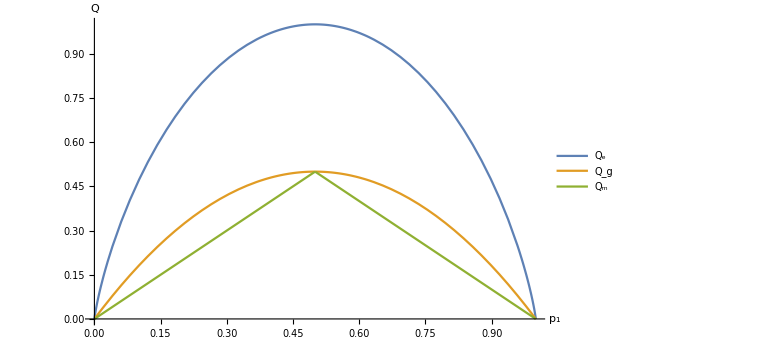

```mathematica
plotMeasures=Plot[{Qe[{p1,1-p1}],Qg[{p1,1-p1}],Qm[{p1,1-p1}]},{p1,0,1},PlotTheme->"myTheme",AxesLabel->{"p_1",it["Q"]},PlotLegends->{"Q_e","Q_g","Q_m"}]
```

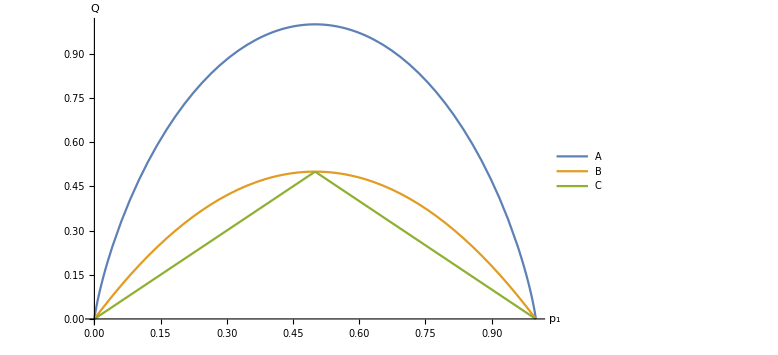

```mathematica
plotMeasures/.{"Q_e"->it["A"],"Q_g"->it["B"],"Q_m"->it["C"]}
```

## Part 2: Examples

```mathematica
Subscript[R, 1]=<|"ω_1"->{{0,0}},"ω_2"->{{0,0.5},{0.5,0},{0,-0.5},{-0.5,0}}|>;
Subscript[R, 2]=<|"ω_1"->{{0,0.5},{0.5,0},{0,-0.5},{-0.5,0}},"ω_2"->{{0,0}}|>;
Subscript[R, 3]=<|"ω_1"->{{-0.5,0.5},{0.5,-0.5}},"ω_2"->{{-0.5,-0.5},{0.5,0.5}}|>;
Subscript[R, 4]=<|"ω_1"->{{0,0},{0,0.5},{0.5,0.5},{0.5,0},{0.5,-0.5},{0,-0.5},{-0.5,-0.5},{-0.5,0},{-0.5,0.5}},"ω_2"->{}|>;
n=4;
```

```mathematica
plotSets[dataA_,dataB_,title_]:=ListPlot[{Piecewise[{{dataA, Length[dataA]>0}, {None, True}}],Piecewise[{{dataB, Length[dataB]>0}, {None, True}}]},
PlotTheme->"Minimal",
LabelStyle->Directive[FontFamily->"Libertinus Serif",FontSize->20],
AxesStyle->Opacity[0.2],
PlotLegends->{"ω_1","ω_2"},
PlotLabel->title,
ImageSize->Medium
]
```

```mathematica
plots=ConstantArray[0,n];
Do[
plots[[i]]=plotSets[Subscript[R, i]["ω_1"],Subscript[R, i]["ω_2"],Subscript["R",i]]
,{i,1,n}]
```

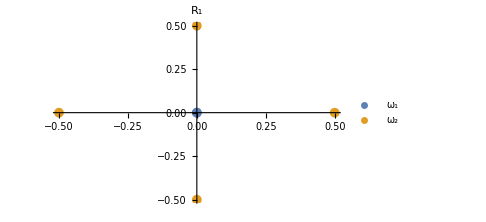
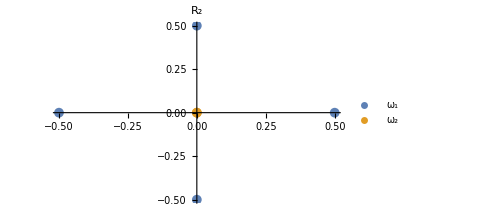
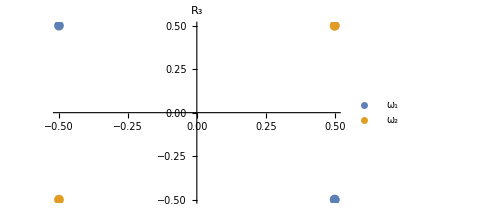
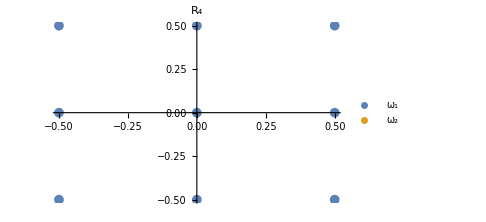

```mathematica
Table[plots[[i]],{i,1,n}]
```

```mathematica
(*Do[
Export[FileNameJoin[{NotebookDirectory[],"Set"<>ToString[p]<>".pdf"}],plots[[p]]]
,{p,1,Length[plots]}]*)
```

```mathematica
probR[R_]:={Length[R["ω_1"]]/(Length[R["ω_1"]]+Length[R["ω_2"]]),Length[R["ω_2"]]/(Length[R["ω_1"]]+Length[R["ω_2"]])}
```

```mathematica
TableForm[
N@Table[
{ToString[probR[Subscript[R, i]],StandardForm],Qm[probR[Subscript[R, i]]],Qg[probR[Subscript[R, i]]],Qe[probR[Subscript[R, i]]]}
,{i,1,n}],
TableHeadings->{
Table[Subscript["R",i],{i,1,n}],
{"p_i","Q_m(p_i)","Q_g(p_i)","Q_e(p_i)"}
}
]
```

| p_i | Q_m(p_i) | Q_g(p_i) | Q_e(p_i)
R_1 | {1/5,4/5} | 0.2 | 0.32 | 0.721928
R_2 | {4/5,1/5} | 0.2 | 0.32 | 0.721928
R_3 | {1/2,1/2} | 0.5 | 0.5 | 1.
R_4 | {1,0} | 0. | 0. | 0.